```mathematica
(* Matrix Dimensions *)
(* From HydrogenIon-2D-6.tex  *) 

Get["/Users/zelimir/Work/Physics-Thesis/thesis-2/MathematicaCode/FindRootsMultiple.m"];

(* Mathieu's eigenvalues, Even and Odd 
Input parameters: p - values of p for which we calculate A
         n - order of the continuous fraction
		  evenOdd - flag to choose even or odd Mathieu's function *)
eigenM[p_,n_Integer,  evenOdd_Integer]:=Module[{w,q,v, A, mCoeffV0, mCoeffV1,rez},
w:=-A +p^2/2.;      q:= -p^2/4.;
v[k_]:=(w-k^2)/q;
mCoeffV0[k_]:=v[0]+2Simplify[ContinuedFractionK[-1,v[2i],{i,1,k}]];
mCoeffV1[k_]:=v[1]-1+Simplify[ContinuedFractionK[-1,v[2i+1],{i,1,k}]];

rez =If[EvenQ[evenOdd],
	NSolve[SetPrecision[mCoeffV0[n]==0,Infinity],{A},Reals],
	NSolve[SetPrecision[mCoeffV1[n]==0,Infinity],{A},Reals]];
rez = Sort[A  /. rez, Abs[#2]> Abs[#1]&];
rez[[1]]
];

(* Create L Matrix 
 Input parameters:    
	    dim - matrix dimensions 
      R - distance betwen nuclei *)
makeLMatrix[dim_, R_]:=Module[{matrix, d,lSum},
d[m_,n_]:=If[n ≥0,KroneckerDelta[m,n],0];
	
lSum[m_,n_] := ((-2)p n(2n+1)-(2p-1)n^2-4p n +(2R-p)(2n+1)-p -p^2+2R)d[m,n]+(2p n(n+1)-(2R-p)(n+1))d[m,n+1]+(2p n^2+(2p-1)n(2n-1) +(4p-2)n -(2R-p)n)d[m,n-1] -(2p-1)n(n-1)d[m,n-2] 
+ Sum[d[m,i],{i,0,n-1}]; 

matrix = Table[Table[(-1)lSum[m,n],{n,0,dim-1}],
{m,0,dim-1}
];
matrix
];

(* Calculate eigenvalues of the M equation 
 Parameters:     pRange - list of all p.
             R - distance between nuclei
              n - order of the continuous fracition
              index - i-th eigenvalue, 1,2,3..
             evenOdd - flag to choose even or odd Mathieu's function *)
calcMEigenvalues[pRange_List, R_, n_Integer,evenOdd_Integer] := Module[{data,a},
data=Map[(a = eigenM[#,n,evenOdd];{#,a}) &, pRange];
data
];

(* Eigenvalues from the L equation 
 Parameters:     pRange - list of all p.
             R - distance between nuclei
              n - order of the continuous fracition
              index - i-th eigenvalue  1,2,3...*)
          
calcLEigenvalues[pRange_List,R_,dim_Integer, index_Integer]:=Module[{matrixL,eigenData,a},
matrixL = makeLMatrix[dim,R] ;
eigenData  = Map[(a = Sort[Select[ Eigenvalues[N[matrixL/.p->#, 40]],Im[#]==0.&]][[index]]; {#,a}) &, pRange];
eigenData
];

(* Calculate electron energy for a given R 
 R - distance between nuclei *)
calcEnergy[R_, index_Integer,evenOdd_Integer]:=Module[
{pRange = Range[0.1,5,.1], nM= 3, nL= 40,
eigenMValues, eigenLValues,mFunc, lFunc,p, ee, am, al, root},

(* returns {p,A} *)
eigenMValues= calcMEigenvalues[pRange, R,nM, evenOdd];
eigenLValues = calcLEigenvalues[pRange, R, nL,index];

       mFunc = Interpolation[eigenMValues, InterpolationOrder->6];
lFunc  =Interpolation[ eigenLValues, InterpolationOrder->6];

p = x /.FindRoot[mFunc[x] == lFunc[x],{x,R}];
(*p= x /. SortBy[FindRoots[mFunc[x] == lFunc[x],{x, 0,2}], Last];*)

(*Print[Plot[{mFunc[x],lFunc[x]},{x,0,5}, PlotStyle->{Red,Green}]];*)

(* values of A  *)
am= mFunc[p];
al= lFunc[p];
ee = -2(p/R)^2;
{R, p, am, ee, ee + 1/R, al}
];

allRs = Table[0.2+i*0.1,{i,0,9}];
allRs = Join[allRs, Table[1+.5*i,{i,1,8}]];
allRs = Join[allRs, Table[5+i,{i,1,5}]];

geradePotential1s= Map[calcEnergy[#1,1,0] &, allRs];

unGeradePotential1s= Map[calcEnergy[#1,1,1] &, allRs];

geradePotential2p= Map[calcEnergy[#1,2,0] &,allRs];

unGeradePotential2p= Map[calcEnergy[#1,2,0] &,allRs];

Print["Gerade 1s_g^+:"];
Prepend[geradePotential1s,{"R","p", "Am","E","E+1/r","Al"}] // MatrixForm
DumpSave["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/gerade1s.mx",geradePotential1s];
Print["Ungerade 2p_u^+:"];
Prepend[unGeradePotential1s,{"R","p", "Am","E","E+1/r","Al"}] // MatrixForm
DumpSave["/Users/zelimir/Work/Physics-Thesis/thesis-2/ZelimirOverleaf/MathematicaCodeFinal/ungerade1s.mx",unGeradePotential1s];
Print["gerade 2s_g^+"];
Prepend[geradePotential2p,{"R","p", "Am","E","E+1/r","Al"}] // MatrixForm
Print["ungerade 2p_u"];
Prepend[unGeradePotential2p,{"R","p", "Am","E","E+1/r","Al"}] // MatrixForm
```

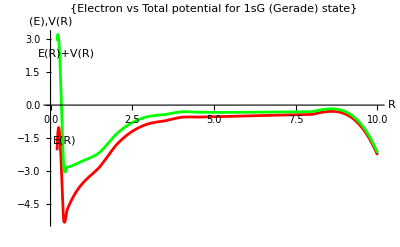

```mathematica
eG = Interpolation[Transpose[{geradePotential1s[[All,1]],geradePotential1s[[All,4]]}]];
eGTotal = Interpolation[Transpose[{geradePotential1s[[All,1]],geradePotential1s[[All,5]]}]];

Plot[{eG[x],eGTotal[x]},{x,0.2,10}, PlotStyle->{Red,Green}, AxesLabel->{"R", "(E),V(R)"}, AxesOrigin->{0,0},PlotLabel->{"Electron vs Total potential for 1sG (Gerade) state"}, PlotLabels->Placed[{"E(R)","E(R)+V(R)"},{Left}], PlotRange->Automatic]
```

```mathematica
totalPotential=Interpolation[Transpose[{outValsEven1[[All,1]],outValsEven1[[All,5]]}]];
totalPotential
Plot[totalPotential[x], {x,.2,10}]
```